```mathematica
H={{-M+Cos[kx]+Cos[ky],-Sin[C*kx]+I*Sin[C*ky]},{-Sin[C*kx]-I*Sin[C*ky],M-Cos[kx]-Cos[ky]}};
H//MatrixForm
```

(-M+Cos[kx]+Cos[ky] | -Sin[C kx]+ⅈ Sin[C ky]
-Sin[C kx]-ⅈ Sin[C ky] | M-Cos[kx]-Cos[ky])

This section evaluates the possible values of M leading to gapless spectrum and lists them in table.

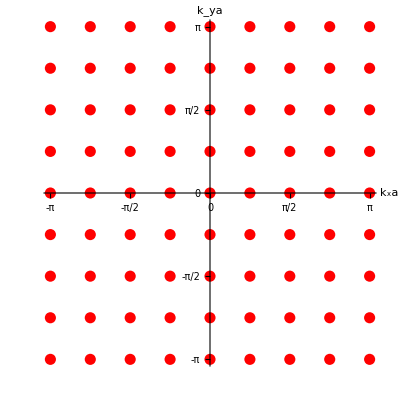

9

9

Power::infy: Infinite expression 1/0 encountered.

{-0.25,-0.292893,-0.5,-1.70711,ComplexInfinity,-0.353553,-0.707107,1.70711,0.707107,0.5,0.353553,0.292893,0.25}

```mathematica
c=4;
tab=Table[
{(n+1)* Pi/c,(m+1)*Pi/c}
,{n,-c-1,c-1},{m,-c-1,c-1}];
tab1=ArrayFlatten[tab];

ListPlot[Flatten[tab1,1],AxesLabel->{"k_xa","k_ya"},AxesStyle->Directive[Black, 12],AspectRatio->1,Ticks->{{-Pi,-Pi/2,0,Pi/2,Pi},{-Pi,-Pi/2,0,Pi/2,Pi}},PlotStyle->{Red,PointSize[.02]}]

d=Dimensions[tab1][[1]]
f[x_,y_]:=Cos[x]+Cos[y];
d=Dimensions[tab][[1]]
m=DeleteDuplicates[
Flatten[
Table[f[tab[[i,j,1]],tab[[i,j,2]]],{i,1,d},{j,1,d}]
]
];
Print[
DeleteDuplicates[
N[1/(2m)]
]]
```

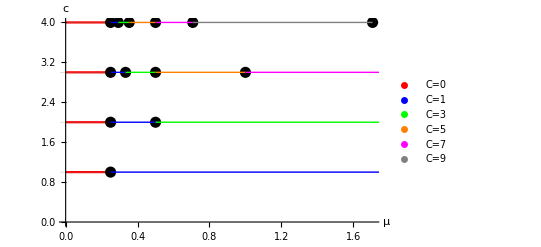

```mathematica
phaseboundaries={
{0.25,1},
{0.25,2},
{0.25,3},
{0.25,4},
{0.5,2},
{0.33333,3},
{0.2928932188134525,4},
{0.5,3},
{0.35355339059327373,4},
{1.,3},
{0.5,4},
{0.7071067811865475,4},
{1.7071067811865472,4}
};
phases0={{
Piecewise[{{1,0<x<0.25}}],
Piecewise[{{2,0<x<0.25}}],
Piecewise[{{3,0<x<0.25}}],
Piecewise[{{4,0<x<0.25}}]
}};
phases1={{
Line[{{0.25,1},{2,1}}],
Line[{{0.25,2},{0.5,2}}],
Line[{{0.25,3},{0.3333,3}}],
Line[{{0.25,4},{0.2929,4}}]
}};
phases2={{
Line[{{0.5,2},{2,2}}],
Line[{{0.3333,3},{0.5,3}}],
Line[{{0.2929,4},{0.3536,4}}]
}};
phases3={{
Line[{{0.5,3},{1.0,3}}],
Line[{{0.3536,4},{0.5,4}}]
}};
phases4={{
Line[{{1.0,3},{2.0,3}}],
Line[{{0.5,4},{0.7071,4}}]
}};
phases5={{
Line[{{0.7071,4},{1.7071,4}}]
}};

leg=LineLegend[{Red,Blue,Green,Orange,Magenta,Gray},{"C=0","C=1","C=3","C=5","C=7","C=9"}];
lp=ListPlot[phaseboundaries,GridLines->{None,{1,2,3,4}},PlotStyle->{Black,PointSize[.02]},AxesLabel->{"μ","c"},AxesStyle->Directive[Black, 12],PlotLegends->leg];
pl0=Plot[phases0,{x,0,0.25},PlotStyle->Red];
pl1=Graphics[{Blue,Thick,phases1}];
pl2=Graphics[{Green,Thick,phases2}];
pl3=Graphics[{Orange,Thick,phases3}];
pl4=Graphics[{Magenta,Thick,phases4}];
pl5=Graphics[{Gray,Thick,phases5}];


Show[lp,pl0,pl1,pl2,pl3,pl4,pl5]
```